# Testing out DMFormFactor functions

```mathematica
SetDirectory["/home/farmer/mathematica/DMFormFactor_13086288"]
```

/home/farmer/mathematica/DMFormFactor_13086288

```mathematica
<<"v6/dmformfactor-V6.m";
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

## Event rate

Model setup

```mathematica
(* Model Setup *)
SetJChi[1/2](* WIMP spin *)
SetMChi[MWIMP GeV] (* WIMP mass in GeV *)
Xe131filename="default";  (* nuclear density matrix (using default density matrices) *)
bFM="default"; (* oscillation parameter (default: approximate formulae used) *)
SetIsotope[54,131,bFM,Xe131filename] (*[Z,A,bFM,filename]*)
ZeroCoeffs[];(*Reset all coefficients*)
SetCoeffsNonrel[1,c1p,"p"]
SetCoeffsNonrel[1,c1n,"n"]
SetCoeffsNonrel[2,c2p,"p"]
SetCoeffsNonrel[2,c2n,"n"]
SetCoeffsNonrel[3,c3p,"p"]
SetCoeffsNonrel[3,c3n,"n"]
SetCoeffsNonrel[4,c4p,"p"]
SetCoeffsNonrel[4,c4n,"n"]
SetCoeffsNonrel[5,c5p,"p"]
SetCoeffsNonrel[5,c5n,"n"]
SetCoeffsNonrel[6,c6p,"p"]
SetCoeffsNonrel[6,c6n,"n"]
SetCoeffsNonrel[7,c7p,"p"]
SetCoeffsNonrel[7,c7n,"n"]
SetCoeffsNonrel[8,c8p,"p"]
SetCoeffsNonrel[8,c8n,"n"]
SetCoeffsNonrel[9,c9p,"p"]
SetCoeffsNonrel[9,c9n,"n"]
SetCoeffsNonrel[10,c10p,"p"]
SetCoeffsNonrel[10,c10n,"n"]
SetCoeffsNonrel[11,c11p,"p"]
SetCoeffsNonrel[11,c11n,"n"]
SetCoeffsNonrel[12,c12p,"p"]
SetCoeffsNonrel[12,c12n,"n"]
SetCoeffsNonrel[13,c13p,"p"]
SetCoeffsNonrel[13,c13n,"n"]
SetCoeffsNonrel[14,c14p,"p"]
SetCoeffsNonrel[14,c14n,"n"]
SetCoeffsNonrel[15,c15p,"p"]
SetCoeffsNonrel[15,c15n,"n"]
(* Set non-zero NR EFT coefficient values *)
```

Getting default matrix...

Setting isotope to xenon-131.

Attempting to compute a recoil spectrum...

```mathematica
(* Parameters *)
mNucleon=0.938 GeV;
NT=1/(131 mNucleon);(*Number of target nuclei per detector mass*)
Centimeter=(10^13 Femtometer);
rhoDM=0.3GeV/Centimeter^3;(*Local dark matter density*)
ve=232 KilometerPerSecond;(*Earth's velocity in galactic rest frame*)
v0=220 KilometerPerSecond;(*Mean WIMP speed in galactic rest frame*)
SetHALO["MB"];(*using default MB Halo*)
```

```mathematica
dRdE=EventRate[NT,rhoDM,qGeV,ve,v0]
```

Your Lagrangian is

L_prot=(0.0000187399 (ⅈ q·S_χ)(v^⊥.(ⅈq×S_N)) c15p)/GeV^4+(0.0000187399 (S_χ·q)(S_N·q) c6p)/GeV^4+(0.0000175831 ⅈ S_N·q c10p)/GeV^3+(0.0000175831 ⅈ S_χ·q c11p)/GeV^3+(0.0000175831 (ⅈq×S_χ)·(S_N·v^⊥) c13p)/GeV^3+(0.0000175831 (ⅈ q·S_χ)(v^⊥·S_N) c14p)/GeV^3+(0.0000175831 ⅈ S_N·(q×v^⊥) c3p)/GeV^3+(0.0000175831 ⅈ S_χ·(q×v^⊥) c5p)/GeV^3+(0.0000175831 ⅈ S_χ.(S_N×q) c9p)/GeV^3+(0.0000164977 S_χ·(S_N×v^⊥) c12p)/GeV^2+(0.0000164977 1 c1p)/GeV^2+(0.0000164977 (v^⊥)^2 c2p)/GeV^2+(0.0000164977 S_χ·S_N c4p)/GeV^2+(0.0000164977 S_N·v^⊥ c7p)/GeV^2+(0.0000164977 S_χ·v^⊥ c8p)/GeV^2

L_neut=(0.0000187399 (ⅈ q·S_χ)(v^⊥.(ⅈq×S_N)) c15n)/GeV^4+(0.0000187399 (S_χ·q)(S_N·q) c6n)/GeV^4+(0.0000175831 ⅈ S_N·q c10n)/GeV^3+(0.0000175831 ⅈ S_χ·q c11n)/GeV^3+(0.0000175831 (ⅈq×S_χ)·(S_N·v^⊥) c13n)/GeV^3+(0.0000175831 (ⅈ q·S_χ)(v^⊥·S_N) c14n)/GeV^3+(0.0000175831 ⅈ S_N·(q×v^⊥) c3n)/GeV^3+(0.0000175831 ⅈ S_χ·(q×v^⊥) c5n)/GeV^3+(0.0000175831 ⅈ S_χ.(S_N×q) c9n)/GeV^3+(0.0000164977 S_χ·(S_N×v^⊥) c12n)/GeV^2+(0.0000164977 1 c1n)/GeV^2+(0.0000164977 (v^⊥)^2 c2n)/GeV^2+(0.0000164977 S_χ·S_N c4n)/GeV^2+(0.0000164977 S_N·v^⊥ c7n)/GeV^2+(0.0000164977 S_χ·v^⊥ c8n)/GeV^2

Warning: Implementation of O_2 discards v_N^2 piece.

Your event rate is

1/(GeV MWIMP^3)2.6053×10^-44 (646.112 ⅇ^(-67.4762 qGeV^2) (0.223035 qGeV^2 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c13p^2 MWIMP^2 qGeV^2) (0.0798479+0.605014 qGeV^2-53.138 qGeV^4+262.736 qGeV^6-0.0000142182 qGeV^8)^2+0.223035 qGeV^2 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c13n^2 MWIMP^2 qGeV^2) (0.516607-22.1809 qGeV^2+263.486 qGeV^4-1294.83 qGeV^6+1311.43 qGeV^8)^2+0.141988 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c13n c13p MWIMP^2 qGeV^2) (-0.129591+4.58215 qGeV^2+62.3055 qGeV^4-4305.25 qGeV^6+64426.2 qGeV^8-436132. qGeV^10+1.28769×10^6 qGeV^12-1.08247×10^6 qGeV^14+0.0585786 qGeV^16)+(0.266447 GeV ((4.08598×10^-9 c4p c5p MWIMP^2)/GeV-(4.08598×10^-9 c8p c9p MWIMP^2)/GeV) qGeV^2+(7.20622×10^-14 c2p c3p (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2) (0.00160907-0.274616 qGeV^2+5.35326 qGeV^4+188.744 qGeV^6-7857.19 qGeV^8+102543. qGeV^10-567802. qGeV^12+1.13687×10^6 qGeV^14-14.3099 qGeV^16+0.0000454276 qGeV^18)+(0.266447 GeV ((4.08598×10^-9 c4n c5p MWIMP^2)/GeV-(4.08598×10^-9 c8p c9n MWIMP^2)/GeV) qGeV^2+(7.20622×10^-14 c2p c3n (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2) (0.0626746-12.4529 qGeV^2+816.667 qGeV^4-26193.6 qGeV^6+453298. qGeV^8-4.27212×10^6 qGeV^10+2.04296×10^7 qGeV^12-3.82971×10^7 qGeV^14-3.63158×10^6 qGeV^16+24.4556 qGeV^18)+(0.266447 GeV ((4.08598×10^-9 c4p c5n MWIMP^2)/GeV-(4.08598×10^-9 c8n c9p MWIMP^2)/GeV) qGeV^2+(7.20622×10^-14 c2n c3p (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2) (0.00804988-1.39694 qGeV^2+30.5161 qGeV^4+767.591 qGeV^6-49133.4 qGeV^8+860740. qGeV^10-6.1233×10^6 qGeV^12+1.57859×10^7 qGeV^14-4.2049×10^6 qGeV^16+24.4556 qGeV^18)+(0.266447 GeV ((4.08598×10^-9 c4n c5n MWIMP^2)/GeV-(4.08598×10^-9 c8n c9n MWIMP^2)/GeV) qGeV^2+(7.20622×10^-14 c2n c3n (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2) (0.31355-63.199 qGeV^2+4351.6 qGeV^4-157684. qGeV^6+3.26796×10^6 qGeV^8-3.79559×10^7 qGeV^10+2.25918×10^8 qGeV^12-5.50605×10^8 qGeV^14+9.9853×10^7 qGeV^16+1.33494×10^7 qGeV^18)+(201.935-21488.2 qGeV^2+888868. qGeV^4-1.84641×10^7 qGeV^6+2.11327×10^8 qGeV^8-1.3687×10^9 qGeV^10+4.91456×10^9 qGeV^12-8.96637×10^9 qGeV^14+6.45128×10^9 qGeV^16) (1.23666×10^-9 c3n^2 MWIMP^2 qGeV^4+0.0709941 qGeV^2 (0.0000619174 c12n MWIMP-0.0000703324 c15n MWIMP qGeV^2)^2)+2 (145.179-13580.4 qGeV^2+488429. qGeV^4-8.70932×10^6 qGeV^6+8.34711×10^7 qGeV^8-4.30669×10^8 qGeV^10+1.10482×10^9 qGeV^12-1.07444×10^9 qGeV^14+933.526 qGeV^16) (1.23666×10^-9 c3n c3p MWIMP^2 qGeV^4+0.0709941 qGeV^2 (0.0000619174 c12n MWIMP-0.0000703324 c15n MWIMP qGeV^2) (0.0000619174 c12p MWIMP-0.0000703324 c15p MWIMP qGeV^2))+(104.803-8490.45 qGeV^2+263668. qGeV^4-3.98191×10^6 qGeV^6+3.1089×10^7 qGeV^8-1.20073×10^8 qGeV^10+1.81321×10^8 qGeV^12-314.895 qGeV^14+0.000136721 qGeV^16) (1.23666×10^-9 c3p^2 MWIMP^2 qGeV^4+0.0709941 qGeV^2 (0.0000619174 c12p MWIMP-0.0000703324 c15p MWIMP qGeV^2)^2)+(0.559596-48.5209 qGeV^2+2053.49 qGeV^4-48572.5 qGeV^6+665153. qGeV^8-4.71895×10^6 qGeV^10+1.42707×10^7 qGeV^12-7.3766×10^6 qGeV^14+1.05877×10^6 qGeV^16) (-(1.44124×10^-13 c2n^2 (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2+0.283977 qGeV^2 (3.83376×10^-9 c8n^2 MWIMP^2+4.3548×10^-9 c5n^2 MWIMP^2 qGeV^2))+2 (0.111856-9.37791 qGeV^2+352.965 qGeV^4-7196.74 qGeV^6+80309.1 qGeV^8-456971. qGeV^10+1.07816×10^6 qGeV^12-288545. qGeV^14+1.9461 qGeV^16) (-(1.44124×10^-13 c2n c2p (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2+0.283977 qGeV^2 (3.83376×10^-9 c8n c8p MWIMP^2+4.3548×10^-9 c5n c5p MWIMP^2 qGeV^2))+(0.0223585-1.8104 qGeV^2+59.7764 qGeV^4-1012.75 qGeV^6+9223.45 qGeV^8-42699.9 qGeV^10+78901.5 qGeV^12-1.06781 qGeV^14+3.62403×10^-6 qGeV^16) (-(1.44124×10^-13 c2p^2 (122.914 GeV+GeV MWIMP)^2 qGeV^4)/GeV^2+0.283977 qGeV^2 (3.83376×10^-9 c8p^2 MWIMP^2+4.3548×10^-9 c5p^2 MWIMP^2 qGeV^2))+(-1092.61+136660. qGeV^2-6.69697×10^6 qGeV^4+1.67374×10^8 qGeV^6-2.3488×10^9 qGeV^8+1.91238×10^10 qGeV^10-8.93828×10^10 qGeV^12+2.25368×10^11 qGeV^14-2.6101×10^11 qGeV^16+8.70616×10^10 qGeV^18) (0.0000175831 c11n MWIMP qGeV^2 (0.0000619174 c12n MWIMP-0.0000703324 c15n MWIMP qGeV^2)+0.0000703324 c3n MWIMP qGeV^2 (0.0000619174 c1n MWIMP-(1.0246×10^-9 c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(-788.171+88535.2 qGeV^2-3.83095×10^6 qGeV^4+8.34616×10^7 qGeV^6-1.00003×10^9 qGeV^8+6.69854×10^9 qGeV^10-2.38915×10^10 qGeV^12+3.83802×10^10 qGeV^14-1.44998×10^10 qGeV^16+12598.1 qGeV^18) (0.0000175831 c11n MWIMP qGeV^2 (0.0000619174 c12p MWIMP-0.0000703324 c15p MWIMP qGeV^2)+0.0000703324 c3p MWIMP qGeV^2 (0.0000619174 c1n MWIMP-(1.0246×10^-9 c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(-766.296+87381.7 qGeV^2-3.85542×10^6 qGeV^4+8.50187×10^7 qGeV^6-1.02681×10^9 qGeV^8+6.95791×10^9 qGeV^10-2.58068×10^10 qGeV^12+4.78309×10^10 qGeV^14-3.44354×10^10 qGeV^16+12598.1 qGeV^18) (0.0000175831 c11p MWIMP qGeV^2 (0.0000619174 c12n MWIMP-0.0000703324 c15n MWIMP qGeV^2)+0.0000703324 c3n MWIMP qGeV^2 (0.0000619174 c1p MWIMP-(1.0246×10^-9 c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(-552.779+55988.5 qGeV^2-2.15745×10^6 qGeV^4+4.09181×10^7 qGeV^6-4.1376×10^8 qGeV^8+2.23042×10^9 qGeV^10-5.88876×10^9 qGeV^12+5.71999×10^9 qGeV^14-7095.2 qGeV^16+0.00184509 qGeV^18) (0.0000175831 c11p MWIMP qGeV^2 (0.0000619174 c12p MWIMP-0.0000703324 c15p MWIMP qGeV^2)+0.0000703324 c3p MWIMP qGeV^2 (0.0000619174 c1p MWIMP-(1.0246×10^-9 c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(0.0878436+9.96911 qGeV^2-264.17 qGeV^4-17861.1 qGeV^6+1.61079×10^6 qGeV^8-4.68721×10^7 qGeV^10+6.461×10^8 qGeV^12-4.27656×10^9 qGeV^14+1.11665×10^10 qGeV^16-4.34684×10^8 qGeV^18+4.29089×10^6 qGeV^20) (1.0887×10^-9 c10n^2 MWIMP^2 qGeV^2+1/16 (3.83376×10^-9 c4n^2 MWIMP^2+8.70959×10^-9 c4n c6n MWIMP^2 qGeV^2+4.94664×10^-9 c6n^2 MWIMP^2 qGeV^4-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c13n^2 MWIMP^2 qGeV^2)))+(0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20) (1.0887×10^-9 c10n c10p MWIMP^2 qGeV^2+1/16 (3.83376×10^-9 c4n c4p MWIMP^2+8.70959×10^-9 c4p c6n MWIMP^2 qGeV^2+4.94664×10^-9 c6n c6p MWIMP^2 qGeV^4-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c13n c13p MWIMP^2 qGeV^2)))+(0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20) (1.0887×10^-9 c10n c10p MWIMP^2 qGeV^2+1/16 (3.83376×10^-9 c4n c4p MWIMP^2+8.70959×10^-9 c4n c6p MWIMP^2 qGeV^2+4.94664×10^-9 c6n c6p MWIMP^2 qGeV^4-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c13n c13p MWIMP^2 qGeV^2)))+(0.0000578995-0.00110472 qGeV^2+0.145001 qGeV^4-23.9866 qGeV^6+1134.14 qGeV^8-23107.7 qGeV^10+224088. qGeV^12-984096. qGeV^14+1.57479×10^6 qGeV^16-5.92859 qGeV^18+0.0000113549 qGeV^20) (1.0887×10^-9 c10p^2 MWIMP^2 qGeV^2+1/16 (3.83376×10^-9 c4p^2 MWIMP^2+8.70959×10^-9 c4p c6p MWIMP^2 qGeV^2+4.94664×10^-9 c6p^2 MWIMP^2 qGeV^4-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c13p^2 MWIMP^2 qGeV^2)))+(5928.2-851956. qGeV^2+4.86226×10^7 qGeV^4-1.43569×10^9 qGeV^6+2.42258×10^10 qGeV^8-2.42602×10^11 qGeV^10+1.43964×10^12 qGeV^12-4.84312×10^12 qGeV^14+8.236×10^12 qGeV^16-5.41182×10^12 qGeV^18+1.17492×10^12 qGeV^20) (3.83376×10^-9 c1n^2 MWIMP^2-(1.26881×10^-13 c1n c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/GeV^2+(1.0498×10^-18 c2n^2 (122.914 GeV+GeV MWIMP)^4 qGeV^4)/(GeV^4 MWIMP^2)+1/4 (4.3548×10^-9 c11n^2 MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c8n^2 MWIMP^2+4.3548×10^-9 c5n^2 MWIMP^2 qGeV^2)))+2 (4157.7-551594. qGeV^2+2.86787×10^7 qGeV^4-7.57984×10^8 qGeV^6+1.12026×10^10 qGeV^8-9.54998×10^10 qGeV^10+4.63347×10^11 qGeV^12-1.19651×10^12 qGeV^14+1.39184×10^12 qGeV^16-4.64714×10^11 qGeV^18+170015. qGeV^20) ((0.0000619174 c1n MWIMP-(1.0246×10^-9 c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)) (0.0000619174 c1p MWIMP-(1.0246×10^-9 c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP))+1/4 (4.3548×10^-9 c11n c11p MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c8n c8p MWIMP^2+4.3548×10^-9 c5n c5p MWIMP^2 qGeV^2)))+(2915.98-354651. qGeV^2+1.66663×10^7 qGeV^4-3.89909×10^8 qGeV^6+4.97028×10^9 qGeV^8-3.52778×10^10 qGeV^10+1.35444×10^11 qGeV^12-2.55168×10^11 qGeV^14+1.83904×10^11 qGeV^16-134154. qGeV^18+0.0248999 qGeV^20) (3.83376×10^-9 c1p^2 MWIMP^2-(1.26881×10^-13 c1p c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/GeV^2+(1.0498×10^-18 c2p^2 (122.914 GeV+GeV MWIMP)^4 qGeV^4)/(GeV^4 MWIMP^2)+1/4 (4.3548×10^-9 c11p^2 MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c8p^2 MWIMP^2+4.3548×10^-9 c5p^2 MWIMP^2 qGeV^2)))+(0.175687-55.5895 qGeV^2+6549.51 qGeV^4-372689. qGeV^6+1.1805×10^7 qGeV^8-2.12171×10^8 qGeV^10+2.11089×10^9 qGeV^12-1.06654×10^10 qGeV^14+2.0847×10^10 qGeV^16+3.72292×10^9 qGeV^18+1.68457×10^8 qGeV^20) (-1/(GeV^2 MWIMP^2)2.06847×10^-6 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c7n^2 MWIMP^2+4.3548×10^-9 c3n^2 MWIMP^2 qGeV^2)+1/32 (7.66753×10^-9 c4n^2 MWIMP^2+8.70959×10^-9 c9n^2 MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c14n^2 MWIMP^2 qGeV^2-8.70959×10^-9 c12n c15n MWIMP^2 qGeV^2+4.94664×10^-9 c15n^2 MWIMP^2 qGeV^4)))+(0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20) (-1/(GeV^2 MWIMP^2)2.06847×10^-6 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c7n c7p MWIMP^2+4.3548×10^-9 c3n c3p MWIMP^2 qGeV^2)+1/32 (7.66753×10^-9 c4n c4p MWIMP^2+8.70959×10^-9 c9n c9p MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c14n c14p MWIMP^2 qGeV^2-8.70959×10^-9 c12p c15n MWIMP^2 qGeV^2+4.94664×10^-9 c15n c15p MWIMP^2 qGeV^4)))+(0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20) (-1/(GeV^2 MWIMP^2)2.06847×10^-6 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c7n c7p MWIMP^2+4.3548×10^-9 c3n c3p MWIMP^2 qGeV^2)+1/32 (7.66753×10^-9 c4n c4p MWIMP^2+8.70959×10^-9 c9n c9p MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c14n c14p MWIMP^2 qGeV^2-8.70959×10^-9 c12n c15p MWIMP^2 qGeV^2+4.94664×10^-9 c15n c15p MWIMP^2 qGeV^4)))+(0.000115799-0.0301499 qGeV^2+1.76061 qGeV^4+57.4599 qGeV^6-897.29 qGeV^8-51856.5 qGeV^10+1.18093×10^6 qGeV^12-7.92115×10^6 qGeV^14+1.70034×10^7 qGeV^16-191.821 qGeV^18+0.000569711 qGeV^20) (-1/(GeV^2 MWIMP^2)2.06847×10^-6 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c7p^2 MWIMP^2+4.3548×10^-9 c3p^2 MWIMP^2 qGeV^2)+1/32 (7.66753×10^-9 c4p^2 MWIMP^2+8.70959×10^-9 c9p^2 MWIMP^2 qGeV^2-1/(GeV^2 MWIMP^2)0.0000165478 (122.914 GeV+GeV MWIMP)^2 qGeV^2 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c14p^2 MWIMP^2 qGeV^2-8.70959×10^-9 c12p c15p MWIMP^2 qGeV^2+4.94664×10^-9 c15p^2 MWIMP^2 qGeV^4)))) (Erf[1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]+Erf[1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)])+0.000733832 ⅇ^(-67.4762 qGeV^2) (8.70959×10^-9 c2p^2 MWIMP^2 qGeV^2 (0.0223585-1.8104 qGeV^2+59.7764 qGeV^4-1012.75 qGeV^6+9223.45 qGeV^8-42699.9 qGeV^10+78901.5 qGeV^12-1.06781 qGeV^14+3.62403×10^-6 qGeV^16)+1.74192×10^-8 c2n c2p MWIMP^2 qGeV^2 (0.111856-9.37791 qGeV^2+352.965 qGeV^4-7196.74 qGeV^6+80309.1 qGeV^8-456971. qGeV^10+1.07816×10^6 qGeV^12-288545. qGeV^14+1.9461 qGeV^16)+8.70959×10^-9 c2n^2 MWIMP^2 qGeV^2 (0.559596-48.5209 qGeV^2+2053.49 qGeV^4-48572.5 qGeV^6+665153. qGeV^8-4.71895×10^6 qGeV^10+1.42707×10^7 qGeV^12-7.3766×10^6 qGeV^14+1.05877×10^6 qGeV^16)-4.3548×10^-9 c2p c3p MWIMP^2 qGeV^2 (0.00160907-0.274616 qGeV^2+5.35326 qGeV^4+188.744 qGeV^6-7857.19 qGeV^8+102543. qGeV^10-567802. qGeV^12+1.13687×10^6 qGeV^14-14.3099 qGeV^16+0.0000454276 qGeV^18)+4.3548×10^-9 c2p c3p MWIMP^2 qGeV^2 (-552.779+55988.5 qGeV^2-2.15745×10^6 qGeV^4+4.09181×10^7 qGeV^6-4.1376×10^8 qGeV^8+2.23042×10^9 qGeV^10-5.88876×10^9 qGeV^12+5.71999×10^9 qGeV^14-7095.2 qGeV^16+0.00184509 qGeV^18)-4.3548×10^-9 c2p c3n MWIMP^2 qGeV^2 (0.0626746-12.4529 qGeV^2+816.667 qGeV^4-26193.6 qGeV^6+453298. qGeV^8-4.27212×10^6 qGeV^10+2.04296×10^7 qGeV^12-3.82971×10^7 qGeV^14-3.63158×10^6 qGeV^16+24.4556 qGeV^18)-4.3548×10^-9 c2n c3p MWIMP^2 qGeV^2 (0.00804988-1.39694 qGeV^2+30.5161 qGeV^4+767.591 qGeV^6-49133.4 qGeV^8+860740. qGeV^10-6.1233×10^6 qGeV^12+1.57859×10^7 qGeV^14-4.2049×10^6 qGeV^16+24.4556 qGeV^18)+4.3548×10^-9 c2p c3n MWIMP^2 qGeV^2 (-766.296+87381.7 qGeV^2-3.85542×10^6 qGeV^4+8.50187×10^7 qGeV^6-1.02681×10^9 qGeV^8+6.95791×10^9 qGeV^10-2.58068×10^10 qGeV^12+4.78309×10^10 qGeV^14-3.44354×10^10 qGeV^16+12598.1 qGeV^18)+4.3548×10^-9 c2n c3p MWIMP^2 qGeV^2 (-788.171+88535.2 qGeV^2-3.83095×10^6 qGeV^4+8.34616×10^7 qGeV^6-1.00003×10^9 qGeV^8+6.69854×10^9 qGeV^10-2.38915×10^10 qGeV^12+3.83802×10^10 qGeV^14-1.44998×10^10 qGeV^16+12598.1 qGeV^18)-4.3548×10^-9 c2n c3n MWIMP^2 qGeV^2 (0.31355-63.199 qGeV^2+4351.6 qGeV^4-157684. qGeV^6+3.26796×10^6 qGeV^8-3.79559×10^7 qGeV^10+2.25918×10^8 qGeV^12-5.50605×10^8 qGeV^14+9.9853×10^7 qGeV^16+1.33494×10^7 qGeV^18)+4.3548×10^-9 c2n c3n MWIMP^2 qGeV^2 (-1092.61+136660. qGeV^2-6.69697×10^6 qGeV^4+1.67374×10^8 qGeV^6-2.3488×10^9 qGeV^8+1.91238×10^10 qGeV^10-8.93828×10^10 qGeV^12+2.25368×10^11 qGeV^14-2.6101×10^11 qGeV^16+8.70616×10^10 qGeV^18)+1/16 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c13p^2 MWIMP^2 qGeV^2) (0.0000578995-0.00110472 qGeV^2+0.145001 qGeV^4-23.9866 qGeV^6+1134.14 qGeV^8-23107.7 qGeV^10+224088. qGeV^12-984096. qGeV^14+1.57479×10^6 qGeV^16-5.92859 qGeV^18+0.0000113549 qGeV^20)+1/8 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c13n c13p MWIMP^2 qGeV^2) (0.00225524+0.106455 qGeV^2-12.073 qGeV^4-29.6556 qGeV^6+24984.9 qGeV^8-773389. qGeV^10+9.78397×10^6 qGeV^12-5.59042×10^7 qGeV^14+1.14708×10^8 qGeV^16-2.13056×10^6 qGeV^18+6.86271 qGeV^20)+1/16 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c13n^2 MWIMP^2 qGeV^2) (0.0878436+9.96911 qGeV^2-264.17 qGeV^4-17861.1 qGeV^6+1.61079×10^6 qGeV^8-4.68721×10^7 qGeV^10+6.461×10^8 qGeV^12-4.27656×10^9 qGeV^14+1.11665×10^10 qGeV^16-4.34684×10^8 qGeV^18+4.29089×10^6 qGeV^20)+(5928.2-851956. qGeV^2+4.86226×10^7 qGeV^4-1.43569×10^9 qGeV^6+2.42258×10^10 qGeV^8-2.42602×10^11 qGeV^10+1.43964×10^12 qGeV^12-4.84312×10^12 qGeV^14+8.236×10^12 qGeV^16-5.41182×10^12 qGeV^18+1.17492×10^12 qGeV^20) (7.66753×10^-9 c1n c2n MWIMP^2-(1.26881×10^-13 c2n^2 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/GeV^2+1/4 (3.83376×10^-9 c8n^2 MWIMP^2+4.3548×10^-9 c5n^2 MWIMP^2 qGeV^2))+(2915.98-354651. qGeV^2+1.66663×10^7 qGeV^4-3.89909×10^8 qGeV^6+4.97028×10^9 qGeV^8-3.52778×10^10 qGeV^10+1.35444×10^11 qGeV^12-2.55168×10^11 qGeV^14+1.83904×10^11 qGeV^16-134154. qGeV^18+0.0248999 qGeV^20) (7.66753×10^-9 c1p c2p MWIMP^2-(1.26881×10^-13 c2p^2 (122.914 GeV+GeV MWIMP)^2 qGeV^2)/GeV^2+1/4 (3.83376×10^-9 c8p^2 MWIMP^2+4.3548×10^-9 c5p^2 MWIMP^2 qGeV^2))+2 (4157.7-551594. qGeV^2+2.86787×10^7 qGeV^4-7.57984×10^8 qGeV^6+1.12026×10^10 qGeV^8-9.54998×10^10 qGeV^10+4.63347×10^11 qGeV^12-1.19651×10^12 qGeV^14+1.39184×10^12 qGeV^16-4.64714×10^11 qGeV^18+170015. qGeV^20) (0.+1/4 (3.83376×10^-9 c8n c8p MWIMP^2+4.3548×10^-9 c5n c5p MWIMP^2 qGeV^2)+0.0000619174 c2p MWIMP (0.0000619174 c1n MWIMP-(1.0246×10^-9 c2n (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP))+0.0000619174 c2n MWIMP (0.0000619174 c1p MWIMP-(1.0246×10^-9 c2p (122.914 GeV+GeV MWIMP)^2 qGeV^2)/(GeV^2 MWIMP)))+(0.175687-55.5895 qGeV^2+6549.51 qGeV^4-372689. qGeV^6+1.1805×10^7 qGeV^8-2.12171×10^8 qGeV^10+2.11089×10^9 qGeV^12-1.06654×10^10 qGeV^14+2.0847×10^10 qGeV^16+3.72292×10^9 qGeV^18+1.68457×10^8 qGeV^20) (1/8 (3.83376×10^-9 c7n^2 MWIMP^2+4.3548×10^-9 c3n^2 MWIMP^2 qGeV^2)+1/32 (3.83376×10^-9 c12n^2 MWIMP^2+4.3548×10^-9 c14n^2 MWIMP^2 qGeV^2-8.70959×10^-9 c12n c15n MWIMP^2 qGeV^2+4.94664×10^-9 c15n^2 MWIMP^2 qGeV^4))+(0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20) (1/8 (3.83376×10^-9 c7n c7p MWIMP^2+4.3548×10^-9 c3n c3p MWIMP^2 qGeV^2)+1/32 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c14n c14p MWIMP^2 qGeV^2-8.70959×10^-9 c12p c15n MWIMP^2 qGeV^2+4.94664×10^-9 c15n c15p MWIMP^2 qGeV^4))+(0.00451048-1.30077 qGeV^2+107.856 qGeV^4-1443.82 qGeV^6-100302. qGeV^8+3.81807×10^6 qGeV^10-5.10723×10^7 qGeV^12+2.91685×10^8 qGeV^14-5.90895×10^8 qGeV^16-5.32206×10^7 qGeV^18+307.518 qGeV^20) (1/8 (3.83376×10^-9 c7n c7p MWIMP^2+4.3548×10^-9 c3n c3p MWIMP^2 qGeV^2)+1/32 (3.83376×10^-9 c12n c12p MWIMP^2+4.3548×10^-9 c14n c14p MWIMP^2 qGeV^2-8.70959×10^-9 c12n c15p MWIMP^2 qGeV^2+4.94664×10^-9 c15n c15p MWIMP^2 qGeV^4))+(0.000115799-0.0301499 qGeV^2+1.76061 qGeV^4+57.4599 qGeV^6-897.29 qGeV^8-51856.5 qGeV^10+1.18093×10^6 qGeV^12-7.92115×10^6 qGeV^14+1.70034×10^7 qGeV^16-191.821 qGeV^18+0.000569711 qGeV^20) (1/8 (3.83376×10^-9 c7p^2 MWIMP^2+4.3548×10^-9 c3p^2 MWIMP^2 qGeV^2)+1/32 (3.83376×10^-9 c12p^2 MWIMP^2+4.3548×10^-9 c14p^2 MWIMP^2 qGeV^2-8.70959×10^-9 c12p c15p MWIMP^2 qGeV^2+4.94664×10^-9 c15p^2 MWIMP^2 qGeV^4))) (0.267504 (-ⅇ^(-(1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))^2) (-1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))+ⅇ^(-(1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP))^2) (1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)))+0.764342 (Erf[1.05455-(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)]+Erf[1.05455+(5.54336 (122.914 GeV+GeV MWIMP) qGeV)/(GeV MWIMP)])))

```mathematica
dRdEsimp=Simplify[dRdE,{Element[GeV,Reals],GeV>0,Element[MWIMP,Reals],MWIMP>0,Element[qGeV,Reals],qGeV>0}];
```

```mathematica
fdRdE[q_]:=dRdE/.qGeV->q;
```

```mathematica
fdRdE[0.1]GeV*2500KilogramDay/.MWIMP->(150(*GeV*))
```

1.42103×10^9 (0.000505338 (0.0097051 (0.0000862597 c12n^2+9.79829×10^-7 c13n^2)+0.000283073 (0.0000862597 c12n c12p+9.79829×10^-7 c13n c13p)+2.91318×10^-6 (0.0000862597 c12p^2+9.79829×10^-7 c13p^2)+4.6514×10^-7 c2n^2+1.83953×10^-7 c2n c2p+1.82394×10^-8 c2p^2-0.000244946 c2n c3n-0.000198511 c2p c3n-0.000207532 c2n c3p-0.000168179 c2p c3p+0.000893815 (1/32 (0.0000862597 c12n^2+9.79829×10^-7 c14n^2-1.95966×10^-6 c12n c15n+1.11299×10^-8 c15n^2)+1/8 (9.79829×10^-7 c3n^2+0.0000862597 c7n^2))+0.000175163 (1/32 (0.0000862597 c12n c12p+9.79829×10^-7 c14n c14p-1.95966×10^-6 c12p c15n+1.11299×10^-8 c15n c15p)+1/8 (9.79829×10^-7 c3n c3p+0.0000862597 c7n c7p))+0.000175163 (1/32 (0.0000862597 c12n c12p+9.79829×10^-7 c14n c14p-1.95966×10^-6 c12n c15p+1.11299×10^-8 c15n c15p)+1/8 (9.79829×10^-7 c3n c3p+0.0000862597 c7n c7p))+0.000034766 (1/32 (0.0000862597 c12p^2+9.79829×10^-7 c14p^2-1.95966×10^-6 c12p c15p+1.11299×10^-8 c15p^2)+1/8 (9.79829×10^-7 c3p^2+0.0000862597 c7p^2))+1054.6 (0.000172519 c1n c2n-9.4503×10^-11 c2n^2+1/4 (9.79829×10^-7 c5n^2+0.0000862597 c8n^2))+1709.15 (0.+0.00928761 c2n (0.00928761 c1p-5.08759×10^-9 c2p)+0.00928761 (0.00928761 c1n-5.08759×10^-9 c2n) c2p+1/4 (9.79829×10^-7 c5n c5p+0.0000862597 c8n c8p))+692.49 (0.000172519 c1p c2p-9.4503×10^-11 c2p^2+1/4 (9.79829×10^-7 c5p^2+0.0000862597 c8p^2)))+344.948 (0.000228195 (0.0000862597 c12n^2+9.79829×10^-7 c13n^2)-0.000115354 (0.0000862597 c12n c12p+9.79829×10^-7 c13n c13p)+0.0000145781 (0.0000862597 c12p^2+9.79829×10^-7 c13p^2)-250.001 (0.0000263746 c11n (0.00928761 c12n-0.000105499 c15n)+0.000105499 (0.00928761 c1n-5.08759×10^-9 c2n) c3n)-202.599 (0.0000263746 c11p (0.00928761 c12n-0.000105499 c15n)+0.000105499 (0.00928761 c1p-5.08759×10^-9 c2p) c3n)+59.457 (0.000709941 (0.00928761 c12n-0.000105499 c15n)^2+2.78248×10^-9 c3n^2)-211.807 (0.0000263746 c11n (0.00928761 c12p-0.000105499 c15p)+0.000105499 (0.00928761 c1n-5.08759×10^-9 c2n) c3p)-171.641 (0.0000263746 c11p (0.00928761 c12p-0.000105499 c15p)+0.000105499 (0.00928761 c1p-5.08759×10^-9 c2p) c3p)+100.603 (0.000709941 (0.00928761 c12n-0.000105499 c15n) (0.00928761 c12p-0.000105499 c15p)+2.78248×10^-9 c3n c3p)+42.5825 (0.000709941 (0.00928761 c12p-0.000105499 c15p)^2+2.78248×10^-9 c3p^2)+0.155282 (2.44957×10^-7 c10n^2+1/16 (-5.47782×10^-7 (0.0000862597 c12n^2+9.79829×10^-7 c13n^2)+0.0000862597 c4n^2+1.95966×10^-6 c4n c6n+1.11299×10^-8 c6n^2))+0.00226459 (2.44957×10^-7 c10n c10p+1/16 (-5.47782×10^-7 (0.0000862597 c12n c12p+9.79829×10^-7 c13n c13p)+0.0000862597 c4n c4p+1.95966×10^-6 c4p c6n+1.11299×10^-8 c6n c6p))+0.00226459 (2.44957×10^-7 c10n c10p+1/16 (-5.47782×10^-7 (0.0000862597 c12n c12p+9.79829×10^-7 c13n c13p)+0.0000862597 c4n c4p+1.95966×10^-6 c4n c6p+1.11299×10^-8 c6n c6p))+0.0000466109 (2.44957×10^-7 c10p^2+1/16 (-5.47782×10^-7 (0.0000862597 c12p^2+9.79829×10^-7 c13p^2)+0.0000862597 c4p^2+1.95966×10^-6 c4p c6p+1.11299×10^-8 c6p^2))+0.237357 (-1.07347×10^-12 c2n^2+0.00283977 (9.79829×10^-7 c5n^2+0.0000862597 c8n^2))+1054.6 (0.0000862597 c1n^2-9.4503×10^-11 c1n c2n+2.58835×10^-17 c2n^2+1/4 (9.79829×10^-7 c11n^2-5.47782×10^-7 (9.79829×10^-7 c5n^2+0.0000862597 c8n^2)))+0.09387 (-1.07347×10^-12 c2n c2p+0.00283977 (9.79829×10^-7 c5n c5p+0.0000862597 c8n c8p))+0.00930743 (-1.07347×10^-12 c2p^2+0.00283977 (9.79829×10^-7 c5p^2+0.0000862597 c8p^2))+1709.15 ((0.00928761 c1n-5.08759×10^-9 c2n) (0.00928761 c1p-5.08759×10^-9 c2p)+1/4 (9.79829×10^-7 c11n c11p-5.47782×10^-7 (9.79829×10^-7 c5n c5p+0.0000862597 c8n c8p)))+692.49 (0.0000862597 c1p^2-9.4503×10^-11 c1p c2p+2.58835×10^-17 c2p^2+1/4 (9.79829×10^-7 c11p^2-5.47782×10^-7 (9.79829×10^-7 c5p^2+0.0000862597 c8p^2)))+0.000893815 (-6.84728×10^-8 (9.79829×10^-7 c3n^2+0.0000862597 c7n^2)+1/32 (-5.47782×10^-7 (0.0000862597 c12n^2+9.79829×10^-7 c14n^2-1.95966×10^-6 c12n c15n+1.11299×10^-8 c15n^2)+0.000172519 c4n^2+1.95966×10^-6 c9n^2))+0.000175163 (-6.84728×10^-8 (9.79829×10^-7 c3n c3p+0.0000862597 c7n c7p)+1/32 (-5.47782×10^-7 (0.0000862597 c12n c12p+9.79829×10^-7 c14n c14p-1.95966×10^-6 c12p c15n+1.11299×10^-8 c15n c15p)+0.000172519 c4n c4p+1.95966×10^-6 c9n c9p))+0.000175163 (-6.84728×10^-8 (9.79829×10^-7 c3n c3p+0.0000862597 c7n c7p)+1/32 (-5.47782×10^-7 (0.0000862597 c12n c12p+9.79829×10^-7 c14n c14p-1.95966×10^-6 c12n c15p+1.11299×10^-8 c15n c15p)+0.000172519 c4n c4p+1.95966×10^-6 c9n c9p))+0.000034766 (-6.84728×10^-8 (9.79829×10^-7 c3p^2+0.0000862597 c7p^2)+1/32 (-5.47782×10^-7 (0.0000862597 c12p^2+9.79829×10^-7 c14p^2-1.95966×10^-6 c12p c15p+1.11299×10^-8 c15p^2)+0.000172519 c4p^2+1.95966×10^-6 c9p^2))-0.0118596 (5.36733×10^-13 c2n c3n+0.00266447 ((0.0000919346 c4n c5n)/GeV-(0.0000919346 c8n c9n)/GeV) GeV)-0.00225574 (5.36733×10^-13 c2p c3n+0.00266447 ((0.0000919346 c4n c5p)/GeV-(0.0000919346 c8p c9n)/GeV) GeV)-0.00251155 (5.36733×10^-13 c2n c3p+0.00266447 ((0.0000919346 c4p c5n)/GeV-(0.0000919346 c8n c9p)/GeV) GeV)-0.000481896 (5.36733×10^-13 c2p c3p+0.00266447 ((0.0000919346 c4p c5p)/GeV-(0.0000919346 c8p c9p)/GeV) GeV)))

```mathematica
fdRdE[0.1]GeV*2500KilogramDay/.MWIMP->(150(*GeV*))/.{c1p->1,c1n->1,c2p->1,c2n->1,c3p->1,c3n->1,c4p->1,c4n->1,c5p->1,c5n->1,c6p->1,c6n->1,c7p->1,c7n->1,c8p->1,c8n->1,c9p->1,c9n->1,c10p->1,c10n->1,c11p->1,c11n->1,c12p->1,c12n->1,c13p->1,c13n->1,c14p->1,c14n->1,c15p->1,c15n->1}
```

1.4606×10^11

```mathematica
fplot=Simplify[fdRdE[q]GeV/.MWIMP->(150(*GeV*))/.{c1p->1,c1n->1,c2p->1,c2n->1,c3p->1,c3n->1,c4p->1,c4n->1,c5p->1,c5n->1,c6p->1,c6n->1,c7p->1,c7n->1,c8p->1,c8n->1,c9p->1,c9n->1,c10p->1,c10n->1,c11p->1,c11n->1,c12p->1,c12n->1,c13p->1,c13n->1,c14p->1,c14n->1,c15p->1,c15n->1},GeV>0]
```

ⅇ^(-270.92 q^2) (5.75631×10^-55 ⅇ^((1.05455-10.0857 q)^2)+5.75631×10^-55 ⅇ^((1.05455+10.0857 q)^2)-5.50537×10^-54 ⅇ^((1.05455-10.0857 q)^2) q+5.50537×10^-54 ⅇ^((1.05455+10.0857 q)^2) q-7.74654×10^-53 ⅇ^((1.05455-10.0857 q)^2) q^2-7.74654×10^-53 ⅇ^((1.05455+10.0857 q)^2) q^2+7.40883×10^-52 ⅇ^((1.05455-10.0857 q)^2) q^3-7.40883×10^-52 ⅇ^((1.05455+10.0857 q)^2) q^3+4.11074×10^-51 ⅇ^((1.05455-10.0857 q)^2) q^4+4.11074×10^-51 ⅇ^((1.05455+10.0857 q)^2) q^4-3.93153×10^-50 ⅇ^((1.05455-10.0857 q)^2) q^5+3.93153×10^-50 ⅇ^((1.05455+10.0857 q)^2) q^5-1.11857×10^-49 ⅇ^((1.05455-10.0857 q)^2) q^6-1.11857×10^-49 ⅇ^((1.05455+10.0857 q)^2) q^6+1.06981×10^-48 ⅇ^((1.05455-10.0857 q)^2) q^7-1.06981×10^-48 ⅇ^((1.05455+10.0857 q)^2) q^7+1.72327×10^-48 ⅇ^((1.05455-10.0857 q)^2) q^8+1.72327×10^-48 ⅇ^((1.05455+10.0857 q)^2) q^8-1.64814×10^-47 ⅇ^((1.05455-10.0857 q)^2) q^9+1.64814×10^-47 ⅇ^((1.05455+10.0857 q)^2) q^9-1.55922×10^-47 ⅇ^((1.05455-10.0857 q)^2) q^10-1.55922×10^-47 ⅇ^((1.05455+10.0857 q)^2) q^10+1.49124×10^-46 ⅇ^((1.05455-10.0857 q)^2) q^11-1.49124×10^-46 ⅇ^((1.05455+10.0857 q)^2) q^11+8.25379×10^-47 ⅇ^((1.05455-10.0857 q)^2) q^12+8.25379×10^-47 ⅇ^((1.05455+10.0857 q)^2) q^12-7.89396×10^-46 ⅇ^((1.05455-10.0857 q)^2) q^13+7.89396×10^-46 ⅇ^((1.05455+10.0857 q)^2) q^13-2.43196×10^-46 ⅇ^((1.05455-10.0857 q)^2) q^14-2.43196×10^-46 ⅇ^((1.05455+10.0857 q)^2) q^14+2.32594×10^-45 ⅇ^((1.05455-10.0857 q)^2) q^15-2.32594×10^-45 ⅇ^((1.05455+10.0857 q)^2) q^15+3.49548×10^-46 ⅇ^((1.05455-10.0857 q)^2) q^16+3.49548×10^-46 ⅇ^((1.05455+10.0857 q)^2) q^16-3.34309×10^-45 ⅇ^((1.05455-10.0857 q)^2) q^17+3.34309×10^-45 ⅇ^((1.05455+10.0857 q)^2) q^17-1.70511×10^-46 ⅇ^((1.05455-10.0857 q)^2) q^18-1.70511×10^-46 ⅇ^((1.05455+10.0857 q)^2) q^18+1.63077×10^-45 ⅇ^((1.05455-10.0857 q)^2) q^19-1.63077×10^-45 ⅇ^((1.05455+10.0857 q)^2) q^19+1.40675×10^-47 ⅇ^((1.05455-10.0857 q)^2) q^20+1.40675×10^-47 ⅇ^((1.05455+10.0857 q)^2) q^20-1.34543×10^-46 ⅇ^((1.05455-10.0857 q)^2) q^21+1.34543×10^-46 ⅇ^((1.05455+10.0857 q)^2) q^21+4.97497×10^-48 ⅇ^((1.05455-10.0857 q)^2) q^22+4.97497×10^-48 ⅇ^((1.05455+10.0857 q)^2) q^22-4.75809×10^-47 ⅇ^((1.05455-10.0857 q)^2) q^23+4.75809×10^-47 ⅇ^((1.05455+10.0857 q)^2) q^23+1.0127×10^-52 ⅇ^((1.05455-10.0857 q)^2) q^24+1.0127×10^-52 ⅇ^((1.05455+10.0857 q)^2) q^24-9.68551×10^-52 ⅇ^((1.05455-10.0857 q)^2) q^25+9.68551×10^-52 ⅇ^((1.05455+10.0857 q)^2) q^25+ⅇ^(203.444 q^2) (7.38256×10^-48-9.93584×10^-46 q^2+5.2708×10^-44 q^4-1.43277×10^-42 q^6+2.2024×10^-41 q^8-1.98398×10^-40 q^10+1.04114×10^-39 q^12-3.01101×10^-39 q^14+4.11902×10^-39 q^16-1.59098×10^-39 q^18-1.7235×10^-40 q^20+1.31686×10^-40 q^22-7.71663×10^-45 q^24-1.60078×10^-49 q^26) Erf[1.05455-10.0857 q]+ⅇ^(203.444 q^2) (7.38256×10^-48-9.93584×10^-46 q^2+5.2708×10^-44 q^4-1.43277×10^-42 q^6+2.2024×10^-41 q^8-1.98398×10^-40 q^10+1.04114×10^-39 q^12-3.01101×10^-39 q^14+4.11902×10^-39 q^16-1.59098×10^-39 q^18-1.7235×10^-40 q^20+1.31686×10^-40 q^22-7.71663×10^-45 q^24-1.60078×10^-49 q^26) Erf[1.05455+10.0857 q])

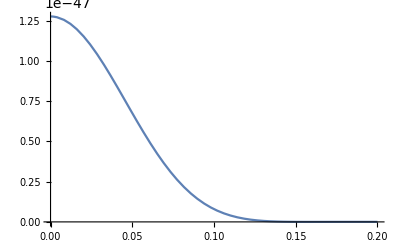

```mathematica
Plot[fplot,{q,0,0.2}]
```

Total predicted number of events for 150 GeV WIMP

```mathematica
2500KilogramDay*NIntegrate[fdRdE[qGeV] GeV*(qGeV GeV/(131 mNucleon))/.MWIMP->(150(*GeV*))/.{c1p->1,c1n->1,c2p->1,c2n->1,c3p->1,c3n->1,c4p->1,c4n->1,c5p->1,c5n->1,c6p->1,c6n->1,c7p->1,c7n->1,c8p->1,c8n->1,c9p->1,c9n->1,c10p->1,c10n->1,c11p->1,c11n->1,c12p->1,c12n->1,c13p->1,c13n->1,c14p->1,c14n->1,c15p->1,c15n->1},{qGeV,0,10}]
```

3.55634×10^7

Total predicted number of events as function of WIMP mass

```mathematica
Plot[2500KilogramDay*NIntegrate[fdRdE[qGeV] GeV*(qGeV GeV/(131 mNucleon))/.MWIMP->(M(*GeV*))/.{c1p->1,c1n->1,c2p->1,c2n->1,c3p->1,c3n->1,c4p->1,c4n->1,c5p->1,c5n->1,c6p->1,c6n->1,c7p->1,c7n->1,c8p->1,c8n->1,c9p->1,c9n->1,c10p->1,c10n->1,c11p->1,c11n->1,c12p->1,c12n->1,c13p->1,c13n->1,c14p->1,c14n->1,c15p->1,c15n->1},{qGeV,0,10}],{M,0,500}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

Recoil spectra for 150 GeV WIMP, for one coupling at a time (coupling values still set to 1)
Note units of (d R_D)/(d E_R) are “event rate per unit time, per unit detector mass, per unit recoil energy”

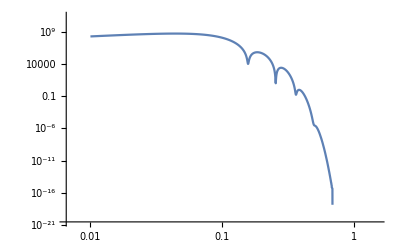

```mathematica
(*as function of q *)
LogLogPlot[2500KilogramDay*fdRdE[qGeV] GeV*(qGeV GeV/(131 mNucleon))/.MWIMP->(150(*GeV*))/.{c1p->1,c1n->1,c2p->1,c2n->1,c3p->1,c3n->1,c4p->1,c4n->1,c5p->1,c5n->1,c6p->1,c6n->1,c7p->1,c7n->1,c8p->1,c8n->1,c9p->1,c9n->1,c10p->1,c10n->1,c11p->1,c11n->1,c12p->1,c12n->1,c13p->1,c13n->1,c14p->1,c14n->1,c15p->1,c15n->1},{qGeV,0.01,1}]
```

Note: E_R = q^2 / 2mT
i.e. q = sqrt( 2*mT*E_R )

```mathematica
(*as function of E_R *)
mT = 131 mNucleon;
2500KilogramDay*fdRdE[√(2mT ER/GeV)] GeV/.MWIMP->(150(*GeV*))/.{c1p->1,c1n->1,c2p->1,c2n->1,c3p->1,c3n->1,c4p->1,c4n->1,c5p->1,c5n->1,c6p->1,c6n->1,c7p->1,c7n->1,c8p->1,c8n->1,c9p->1,c9n->1,c10p->1,c10n->1,c11p->1,c11n->1,c12p->1,c12n->1,c13p->1,c13n->1,c14p->1,c14n->1,c15p->1,c15n->1}
```

1.42103×10^9 (646.112 ⅇ^(-16582.7 ER) (54.8121 (0.0000862597+0.0240799 ER) ER (0.0798479+148.686 ER-3.20932×10^6 ER^2+3.89971×10^9 ER^3-51863.4 ER^4)^2+54.8121 (0.0000862597+0.0240799 ER) ER (0.516607-5451.09 ER+1.59135×10^7 ER^2-1.92187×10^10 ER^3+4.78368×10^12 ER^4)^2+(69.7889 (0.0000862597+0.0240799 ER) ER-0.00064833 ER^2) (0.0223585-444.918 ER+3.61025×10^6 ER^2-1.50319×10^10 ER^3+3.36442×10^13 ER^4-3.82779×10^16 ER^5+1.73824×10^19 ER^6-5.78125×10^16 ER^7+4.82197×10^13 ER^8)+(17.4472 (0.00928761-2.59269 ER)^2 ER+1.68051 ER^2) (104.803-2.08658×10^6 ER+1.59245×10^10 ER^2-5.91022×10^13 ER^3+1.13403×10^17 ER^4-1.07638×10^20 ER^5+3.99459×10^22 ER^6-1.70488×10^19 ER^7+1.81915×10^15 ER^8)+34.8945 (0.0000862597+0.0240799 ER) ER (-0.129591+1126.09 ER+3.763×10^6 ER^2-6.39014×10^10 ER^3+2.35006×10^14 ER^4-3.90966×10^17 ER^5+2.83685×10^20 ER^6-5.86062×10^22 ER^7+7.79421×10^17 ER^8)+2 (69.7889 (0.0000862597+0.0240799 ER) ER-0.00064833 ER^2) (0.111856-2304.68 ER+2.13177×10^7 ER^2-1.06819×10^11 ER^3+2.92942×10^14 ER^4-4.09646×10^17 ER^5+2.37523×10^20 ER^6-1.56222×10^22 ER^7+2.5894×10^19 ER^8)+2 (17.4472 (0.00928761-2.59269 ER)^2 ER+1.68051 ER^2) (145.179-3.33747×10^6 ER+2.94991×10^10 ER^2-1.2927×10^14 ER^3+3.04476×10^17 ER^4-3.86068×10^20 ER^5+2.43398×10^23 ER^6-5.81714×10^25 ER^7+1.24211×10^22 ER^8)+(69.7889 (0.0000862597+0.0240799 ER) ER-0.00064833 ER^2) (0.559596-11924.3 ER+1.24023×10^8 ER^2-7.20947×10^11 ER^3+2.42626×10^15 ER^4-4.23025×10^18 ER^5+3.1439×10^21 ER^6-3.99379×10^23 ER^7+1.40875×10^25 ER^8)+(17.4472 (0.00928761-2.59269 ER)^2 ER+1.68051 ER^2) (201.935-5.28086×10^6 ER+5.36841×10^10 ER^2-2.74057×10^14 ER^3+7.70852×10^17 ER^4-1.22696×10^21 ER^5+1.0827×10^24 ER^6-4.85451×10^26 ER^7+8.58379×10^28 ER^8)+(0.+0.000324165 ER^2) (0.00160907-67.4885 ER+323316. ER^2+2.80147×10^9 ER^3-2.86605×10^13 ER^4+9.19234×10^16 ER^5-1.2509×10^20 ER^6+6.15518×10^22 ER^7-1.90402×10^20 ER^8+1.48545×10^17 ER^9)+(0.648172 (0.00928761-2.59269 ER) ER+2.59269 (0.00928761-0.00012503 ER) ER) (-552.779+1.37595×10^7 ER-1.30301×10^11 ER^2+6.07335×10^14 ER^3-1.50926×10^18 ER^4+1.99944×10^21 ER^5-1.29733×10^24 ER^6+3.09688×10^26 ER^7-9.44056×10^22 ER^8+6.03328×10^18 ER^9)+(0.+0.000324165 ER^2) (0.0626746-3060.38 ER+4.93235×10^7 ER^2-3.88784×10^11 ER^3+1.65349×10^15 ER^4-3.82969×10^18 ER^5+4.50076×10^21 ER^6-2.07346×10^24 ER^7-4.83202×10^25 ER^8+7.99679×10^22 ER^9)+(0.+0.000324165 ER^2) (0.00804988-343.307 ER+1.84305×10^6 ER^2+1.13931×10^10 ER^3-1.79223×10^14 ER^4+7.716×10^17 ER^5-1.34899×10^21 ER^6+8.54669×10^23 ER^7-5.59485×10^25 ER^8+7.99679×10^22 ER^9)+(0.648172 (0.00928761-2.59269 ER) ER+2.59269 (0.00928761-0.00012503 ER) ER) (-766.296+2.14746×10^7 ER-2.32852×10^11 ER^2+1.26191×10^15 ER^3-3.74546×10^18 ER^4+6.23734×10^21 ER^5-5.68536×10^24 ER^6+2.58963×10^27 ER^7-4.58182×10^29 ER^8+4.11949×10^25 ER^9)+(0.648172 (0.00928761-2.59269 ER) ER+2.59269 (0.00928761-0.00012503 ER) ER) (-788.171+2.1758×10^7 ER-2.31374×10^11 ER^2+1.23879×10^15 ER^3-3.64779×10^18 ER^4+6.00483×10^21 ER^5-5.26342×10^24 ER^6+2.07795×10^27 ER^7-1.92928×10^29 ER^8+4.11949×10^25 ER^9)+(0.+0.000324165 ER^2) (0.31355-15531.5 ER+2.62819×10^8 ER^2-2.34046×10^12 ER^3+1.19205×10^16 ER^4-3.40252×10^19 ER^5+4.97709×10^22 ER^6-2.98105×10^25 ER^7+1.3286×10^27 ER^8+4.36516×10^28 ER^9)+(0.648172 (0.00928761-2.59269 ER) ER+2.59269 (0.00928761-0.00012503 ER) ER) (-1092.61+3.35849×10^7 ER-4.0447×10^11 ER^2+2.48429×10^15 ER^3-8.56765×10^18 ER^4+1.71434×10^22 ER^5-1.96915×10^25 ER^6+1.22017×10^28 ER^7-3.47288×10^30 ER^8+2.84684×10^32 ER^9)+2 (4157.7-1.35558×10^8 ER+1.73208×10^12 ER^2-1.12505×10^16 ER^3+4.08636×10^19 ER^4-8.56097×10^22 ER^5+1.02078×10^26 ER^6-6.47808×10^28 ER^7+1.85192×10^31 ER^8-1.51958×10^33 ER^9+1.36624×10^29 ER^10) ((0.00928761-0.00012503 ER)^2+1/4 (0.0240799 ER-0.0134621 (0.0000862597+0.0240799 ER) ER))+(2915.98-8.71577×10^7 ER+1.00658×10^12 ER^2-5.7873×10^15 ER^3+1.813×10^19 ER^4-3.16244×10^22 ER^5+2.98391×10^25 ER^6-1.38151×10^28 ER^7+2.44694×10^30 ER^8-4.38672×10^26 ER^9+2.00096×10^22 ER^10) (0.0000862597-2.32247×10^-6 ER+1.56326×10^-8 ER^2+1/4 (0.0240799 ER-0.0134621 (0.0000862597+0.0240799 ER) ER))+(5928.2-2.09373×10^8 ER+2.93661×10^12 ER^2-2.13095×10^16 ER^3+8.83678×10^19 ER^4-2.17478×10^23 ER^5+3.1716×10^26 ER^6-2.62213×10^29 ER^7+1.09585×10^32 ER^8-1.76962×10^34 ER^9+9.44166×10^35 ER^10) (0.0000862597-2.32247×10^-6 ER+1.56326×10^-8 ER^2+1/4 (0.0240799 ER-0.0134621 (0.0000862597+0.0240799 ER) ER))+(0.0000578995-0.271491 ER+8757.46 ER^2-3.56025×10^8 ER^3+4.13698×10^12 ER^4-2.07147×10^16 ER^5+4.93678×10^19 ER^6-5.32802×10^22 ER^7+2.09535×10^25 ER^8-1.9386×10^22 ER^9+9.12483×10^18 ER^10) (0.00601997 ER+1/16 (0.0000862597+0.0481598 ER-0.0134621 (0.0000862597+0.0240799 ER) ER+6.72204 ER^2))+2 (0.00225524+26.162 ER-729158. ER^2-4.40169×10^8 ER^3+9.1137×10^13 ER^4-6.93296×10^17 ER^5+2.15546×10^21 ER^6-3.02673×10^24 ER^7+1.52625×10^27 ER^8-6.96676×10^27 ER^9+5.51489×10^24 ER^10) (0.00601997 ER+1/16 (0.0000862597+0.0481598 ER-0.0134621 (0.0000862597+0.0240799 ER) ER+6.72204 ER^2))+(0.0878436+2449.97 ER-1.59548×10^7 ER^2-2.65107×10^11 ER^3+5.87564×10^15 ER^4-4.2018×10^19 ER^5+1.42339×10^23 ER^6-2.31539×10^26 ER^7+1.48576×10^29 ER^8-1.42138×10^30 ER^9+3.44817×10^30 ER^10) (0.00601997 ER+1/16 (0.0000862597+0.0481598 ER-0.0134621 (0.0000862597+0.0240799 ER) ER+6.72204 ER^2))+(0.000115799-7.40952 ER+106334. ER^2+8.52859×10^8 ER^3-3.27302×10^12 ER^4-4.64862×10^16 ER^5+2.60166×10^20 ER^6-4.28861×10^23 ER^7+2.2624×10^26 ER^8-6.27238×10^23 ER^9+4.57821×10^20 ER^10) (-0.00168276 (0.0000862597+0.0240799 ER) ER+1/32 (0.000172519+0.0481598 ER-0.0134621 ER (0.0000862597-0.0240799 ER+6.72204 ER^2)))+2 (0.00451048-319.671 ER+6.51407×10^6 ER^2-2.14302×10^10 ER^3-3.65868×10^14 ER^4+3.42267×10^18 ER^5-1.12515×10^22 ER^6+1.57922×10^25 ER^7-7.86219×10^27 ER^8-1.74027×10^29 ER^9+2.47122×10^26 ER^10) (-0.00168276 (0.0000862597+0.0240799 ER) ER+1/32 (0.000172519+0.0481598 ER-0.0134621 ER (0.0000862597-0.0240799 ER+6.72204 ER^2)))+(0.175687-13661.5 ER+3.95565×10^8 ER^2-5.53171×10^12 ER^3+4.3061×10^16 ER^4-1.90198×10^20 ER^5+4.6504×10^23 ER^6-5.77441×10^26 ER^7+2.77381×10^29 ER^8+1.21737×10^31 ER^9+1.35373×10^32 ER^10) (-0.00168276 (0.0000862597+0.0240799 ER) ER+1/32 (0.000172519+0.0481598 ER-0.0134621 ER (0.0000862597-0.0240799 ER+6.72204 ER^2)))) (Erf[1.05455-158.11 √ER]+Erf[1.05455+158.11 √ER])+0.000733832 ⅇ^(-16582.7 ER) (0.0481598 ER (0.0223585-444.918 ER+3.61025×10^6 ER^2-1.50319×10^10 ER^3+3.36442×10^13 ER^4-3.82779×10^16 ER^5+1.73824×10^19 ER^6-5.78125×10^16 ER^7+4.82197×10^13 ER^8)+0.0963195 ER (0.111856-2304.68 ER+2.13177×10^7 ER^2-1.06819×10^11 ER^3+2.92942×10^14 ER^4-4.09646×10^17 ER^5+2.37523×10^20 ER^6-1.56222×10^22 ER^7+2.5894×10^19 ER^8)+0.0481598 ER (0.559596-11924.3 ER+1.24023×10^8 ER^2-7.20947×10^11 ER^3+2.42626×10^15 ER^4-4.23025×10^18 ER^5+3.1439×10^21 ER^6-3.99379×10^23 ER^7+1.40875×10^25 ER^8)-0.0240799 ER (0.00160907-67.4885 ER+323316. ER^2+2.80147×10^9 ER^3-2.86605×10^13 ER^4+9.19234×10^16 ER^5-1.2509×10^20 ER^6+6.15518×10^22 ER^7-1.90402×10^20 ER^8+1.48545×10^17 ER^9)+0.0240799 ER (-552.779+1.37595×10^7 ER-1.30301×10^11 ER^2+6.07335×10^14 ER^3-1.50926×10^18 ER^4+1.99944×10^21 ER^5-1.29733×10^24 ER^6+3.09688×10^26 ER^7-9.44056×10^22 ER^8+6.03328×10^18 ER^9)-0.0240799 ER (0.0626746-3060.38 ER+4.93235×10^7 ER^2-3.88784×10^11 ER^3+1.65349×10^15 ER^4-3.82969×10^18 ER^5+4.50076×10^21 ER^6-2.07346×10^24 ER^7-4.83202×10^25 ER^8+7.99679×10^22 ER^9)-0.0240799 ER (0.00804988-343.307 ER+1.84305×10^6 ER^2+1.13931×10^10 ER^3-1.79223×10^14 ER^4+7.716×10^17 ER^5-1.34899×10^21 ER^6+8.54669×10^23 ER^7-5.59485×10^25 ER^8+7.99679×10^22 ER^9)+0.0240799 ER (-766.296+2.14746×10^7 ER-2.32852×10^11 ER^2+1.26191×10^15 ER^3-3.74546×10^18 ER^4+6.23734×10^21 ER^5-5.68536×10^24 ER^6+2.58963×10^27 ER^7-4.58182×10^29 ER^8+4.11949×10^25 ER^9)+0.0240799 ER (-788.171+2.1758×10^7 ER-2.31374×10^11 ER^2+1.23879×10^15 ER^3-3.64779×10^18 ER^4+6.00483×10^21 ER^5-5.26342×10^24 ER^6+2.07795×10^27 ER^7-1.92928×10^29 ER^8+4.11949×10^25 ER^9)-0.0240799 ER (0.31355-15531.5 ER+2.62819×10^8 ER^2-2.34046×10^12 ER^3+1.19205×10^16 ER^4-3.40252×10^19 ER^5+4.97709×10^22 ER^6-2.98105×10^25 ER^7+1.3286×10^27 ER^8+4.36516×10^28 ER^9)+0.0240799 ER (-1092.61+3.35849×10^7 ER-4.0447×10^11 ER^2+2.48429×10^15 ER^3-8.56765×10^18 ER^4+1.71434×10^22 ER^5-1.96915×10^25 ER^6+1.22017×10^28 ER^7-3.47288×10^30 ER^8+2.84684×10^32 ER^9)+1/16 (0.0000862597+0.0240799 ER) (0.0000578995-0.271491 ER+8757.46 ER^2-3.56025×10^8 ER^3+4.13698×10^12 ER^4-2.07147×10^16 ER^5+4.93678×10^19 ER^6-5.32802×10^22 ER^7+2.09535×10^25 ER^8-1.9386×10^22 ER^9+9.12483×10^18 ER^10)+(0.000172519+1/4 (0.0000862597+0.0240799 ER)-2.32247×10^-6 ER) (2915.98-8.71577×10^7 ER+1.00658×10^12 ER^2-5.7873×10^15 ER^3+1.813×10^19 ER^4-3.16244×10^22 ER^5+2.98391×10^25 ER^6-1.38151×10^28 ER^7+2.44694×10^30 ER^8-4.38672×10^26 ER^9+2.00096×10^22 ER^10)+1/8 (0.0000862597+0.0240799 ER) (0.00225524+26.162 ER-729158. ER^2-4.40169×10^8 ER^3+9.1137×10^13 ER^4-6.93296×10^17 ER^5+2.15546×10^21 ER^6-3.02673×10^24 ER^7+1.52625×10^27 ER^8-6.96676×10^27 ER^9+5.51489×10^24 ER^10)+2 (0.+0.0185752 (0.00928761-0.00012503 ER)+1/4 (0.0000862597+0.0240799 ER)) (4157.7-1.35558×10^8 ER+1.73208×10^12 ER^2-1.12505×10^16 ER^3+4.08636×10^19 ER^4-8.56097×10^22 ER^5+1.02078×10^26 ER^6-6.47808×10^28 ER^7+1.85192×10^31 ER^8-1.51958×10^33 ER^9+1.36624×10^29 ER^10)+1/16 (0.0000862597+0.0240799 ER) (0.0878436+2449.97 ER-1.59548×10^7 ER^2-2.65107×10^11 ER^3+5.87564×10^15 ER^4-4.2018×10^19 ER^5+1.42339×10^23 ER^6-2.31539×10^26 ER^7+1.48576×10^29 ER^8-1.42138×10^30 ER^9+3.44817×10^30 ER^10)+(0.000172519+1/4 (0.0000862597+0.0240799 ER)-2.32247×10^-6 ER) (5928.2-2.09373×10^8 ER+2.93661×10^12 ER^2-2.13095×10^16 ER^3+8.83678×10^19 ER^4-2.17478×10^23 ER^5+3.1716×10^26 ER^6-2.62213×10^29 ER^7+1.09585×10^32 ER^8-1.76962×10^34 ER^9+9.44166×10^35 ER^10)+(0.000115799-7.40952 ER+106334. ER^2+8.52859×10^8 ER^3-3.27302×10^12 ER^4-4.64862×10^16 ER^5+2.60166×10^20 ER^6-4.28861×10^23 ER^7+2.2624×10^26 ER^8-6.27238×10^23 ER^9+4.57821×10^20 ER^10) (1/8 (0.0000862597+0.0240799 ER)+1/32 (0.0000862597-0.0240799 ER+6.72204 ER^2))+2 (0.00451048-319.671 ER+6.51407×10^6 ER^2-2.14302×10^10 ER^3-3.65868×10^14 ER^4+3.42267×10^18 ER^5-1.12515×10^22 ER^6+1.57922×10^25 ER^7-7.86219×10^27 ER^8-1.74027×10^29 ER^9+2.47122×10^26 ER^10) (1/8 (0.0000862597+0.0240799 ER)+1/32 (0.0000862597-0.0240799 ER+6.72204 ER^2))+(0.175687-13661.5 ER+3.95565×10^8 ER^2-5.53171×10^12 ER^3+4.3061×10^16 ER^4-1.90198×10^20 ER^5+4.6504×10^23 ER^6-5.77441×10^26 ER^7+2.77381×10^29 ER^8+1.21737×10^31 ER^9+1.35373×10^32 ER^10) (1/8 (0.0000862597+0.0240799 ER)+1/32 (0.0000862597-0.0240799 ER+6.72204 ER^2))) (0.267504 (-ⅇ^(-(1.05455+158.11 √ER)^2) (-1.05455+158.11 √ER)+ⅇ^(-(1.05455-158.11 √ER)^2) (1.05455+158.11 √ER))+0.764342 (Erf[1.05455-158.11 √ER]+Erf[1.05455+158.11 √ER])))

Note units of (d R_D)/(d E_R) are “event rate per unit time, per unit detector mass, per unit recoil energy”. Multiplying in the exposure in kilogram days gets “event rate per unit recoil energy”
Note also kinematic threshold E_(R,max)=2(μ_T^2 v^2)/m_T, with μ_T=(m_χ m_T)/(m_χ+m_T)(I assume).

0.0000444707

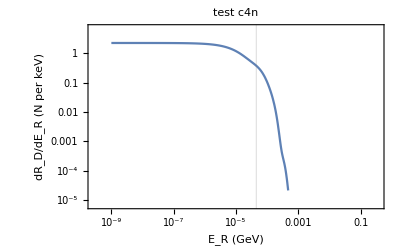

```mathematica
(*as function of E_R *)
mχ=150;(*GeV*)
mT = 131 mNucleon;
μT=(mχ GeV mT)/(mχ GeV+mT);
ERmax = 2(μT^2 v^2)/mT/GeV/.v->ve(*just using earth speed to get rough number, and get rid of GeV units for plotting*)

resttozero={c1p->0,c1n->0,c2p->0,c2n->0,c3p->0,c3n->0,c4p->0,c4n->0,c5p->0,c5n->0,c6p->0,c6n->0,c7p->0,c7n->0,c8p->0,c8n->0,c9p->0,c9n->0,c10p->0,c10n->0,c11p->0,c11n->0,c12p->0,c12n->0,c13p->0,c13n->0,c14p->0,c14n->0,c15p->0,c15n->0};
arg=2500KilogramDay*fdRdE[√(2mT ER/GeV)] GeV/.MWIMP->mχ/.{c4n->1}/.resttozero;
LogLogPlot[10^3*arg*10^-9,{ER,10^-9 ,0.1 },Frame->True ,FrameLabel->{"E_R (GeV)","dR_D/dE_R (N per keV)"},GridLines->{{ERmax},{}},PlotLabel->"test c4n"]
```

```mathematica
(* Grid *)
arg=2500KilogramDay*fdRdE[√(2mT ER/GeV)] GeV/.MWIMP->mχ;

coefflist={c1p,c1n,c2p,c2n,c3p,c3n,c4p,c4n,c5p,c5n,c6p,c6n,c7p,c7n,c8p,c8n,c9p,c9n,c10p,c10n,c11p,c11n,c12p,c12n,c13p,c13n,c14p,c14n,c15p,c15n};
resttozero={c1p->0,c1n->0,c2p->0,c2n->0,c3p->0,c3n->0,c4p->0,c4n->0,c5p->0,c5n->0,c6p->0,c6n->0,c7p->0,c7n->0,c8p->0,c8n->0,c9p->0,c9n->0,c10p->0,c10n->0,c11p->0,c11n->0,c12p->0,c12n->0,c13p->0,c13n->0,c14p->0,c14n->0,c15p->0,c15n->0};
rules=Table[{coefflist⟦i⟧->1},{i,1,30}];
titles=Table[coefflist⟦i⟧,{i,1,30}];
plots=Table[
LogLogPlot[10^3*arg*10^-9/.rules⟦i⟧/.resttozero,{ER,10^-9 ,0.1 },Frame->True ,FrameLabel->{"E_R (GeV)","dR_D/dE_R (N per keV)"},GridLines->{{ERmax},{}},PlotLabel->titles⟦i⟧],{i,1,30}];
```

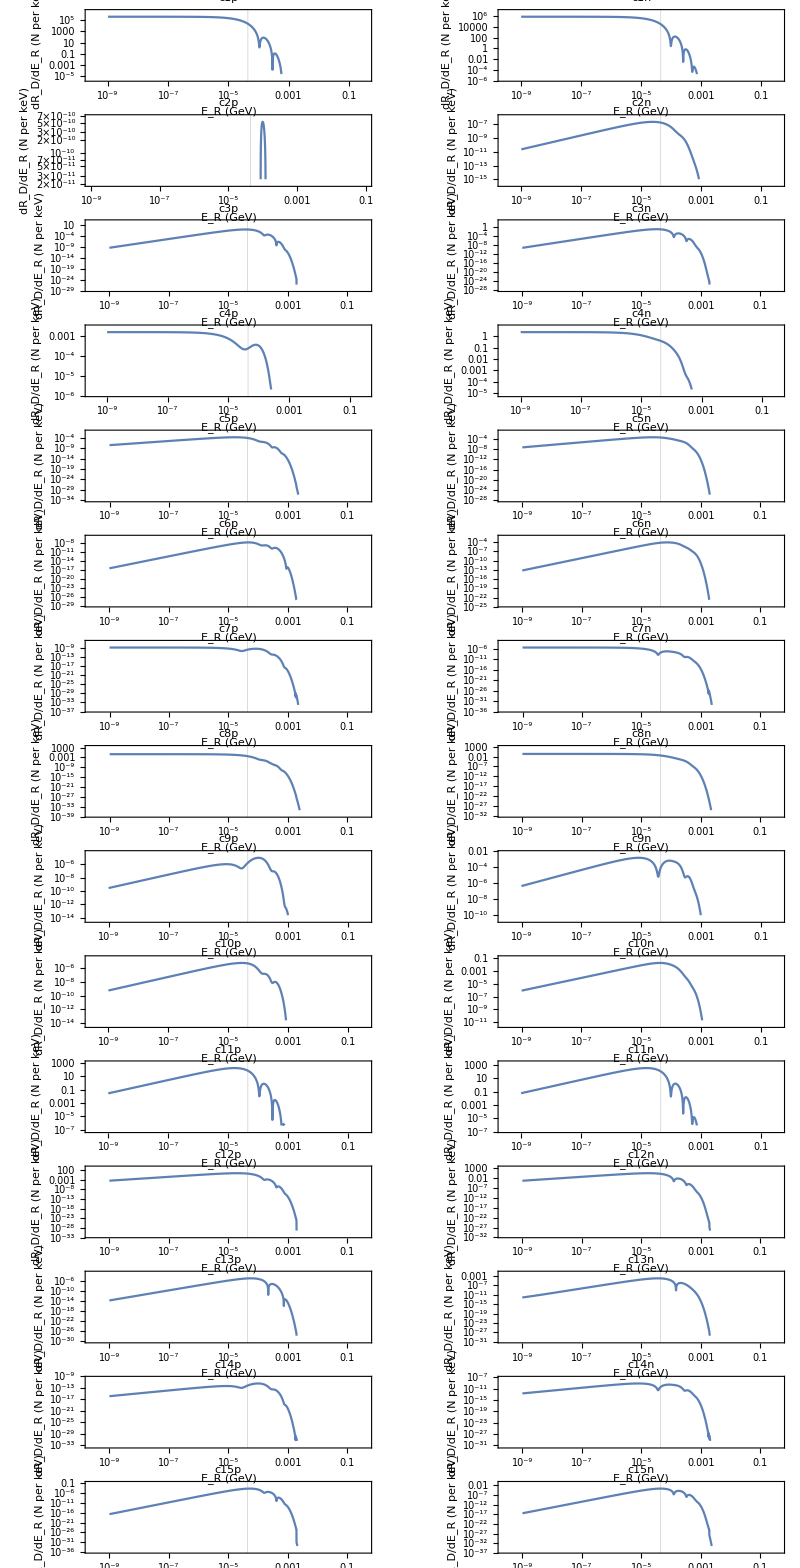

```mathematica
GraphicsGrid[ArrayReshape[plots,{15,2}],ImageSize->Full]
```

```mathematica
(* Non-log scale Grid *)
arg=2500KilogramDay*fdRdE[√(2mT ER/GeV)] GeV/.MWIMP->mχ;

coefflist={c1p,c1n,c2p,c2n,c3p,c3n,c4p,c4n,c5p,c5n,c6p,c6n,c7p,c7n,c8p,c8n,c9p,c9n,c10p,c10n,c11p,c11n,c12p,c12n,c13p,c13n,c14p,c14n,c15p,c15n};
resttozero={c1p->0,c1n->0,c2p->0,c2n->0,c3p->0,c3n->0,c4p->0,c4n->0,c5p->0,c5n->0,c6p->0,c6n->0,c7p->0,c7n->0,c8p->0,c8n->0,c9p->0,c9n->0,c10p->0,c10n->0,c11p->0,c11n->0,c12p->0,c12n->0,c13p->0,c13n->0,c14p->0,c14n->0,c15p->0,c15n->0};
rules=Table[{coefflist⟦i⟧->1},{i,1,30}];
titles=Table[coefflist⟦i⟧,{i,1,30}];
plots=Table[
Plot[10^3*arg*10^-9/.rules⟦i⟧/.resttozero,{ER,0 ,10^-3 },Frame->True ,FrameLabel->{"E_R (GeV)","dR_D/dE_R (N per keV)"},GridLines->{{ERmax},{}},PlotLabel->titles⟦i⟧,PlotRange->All],{i,1,30}];
```

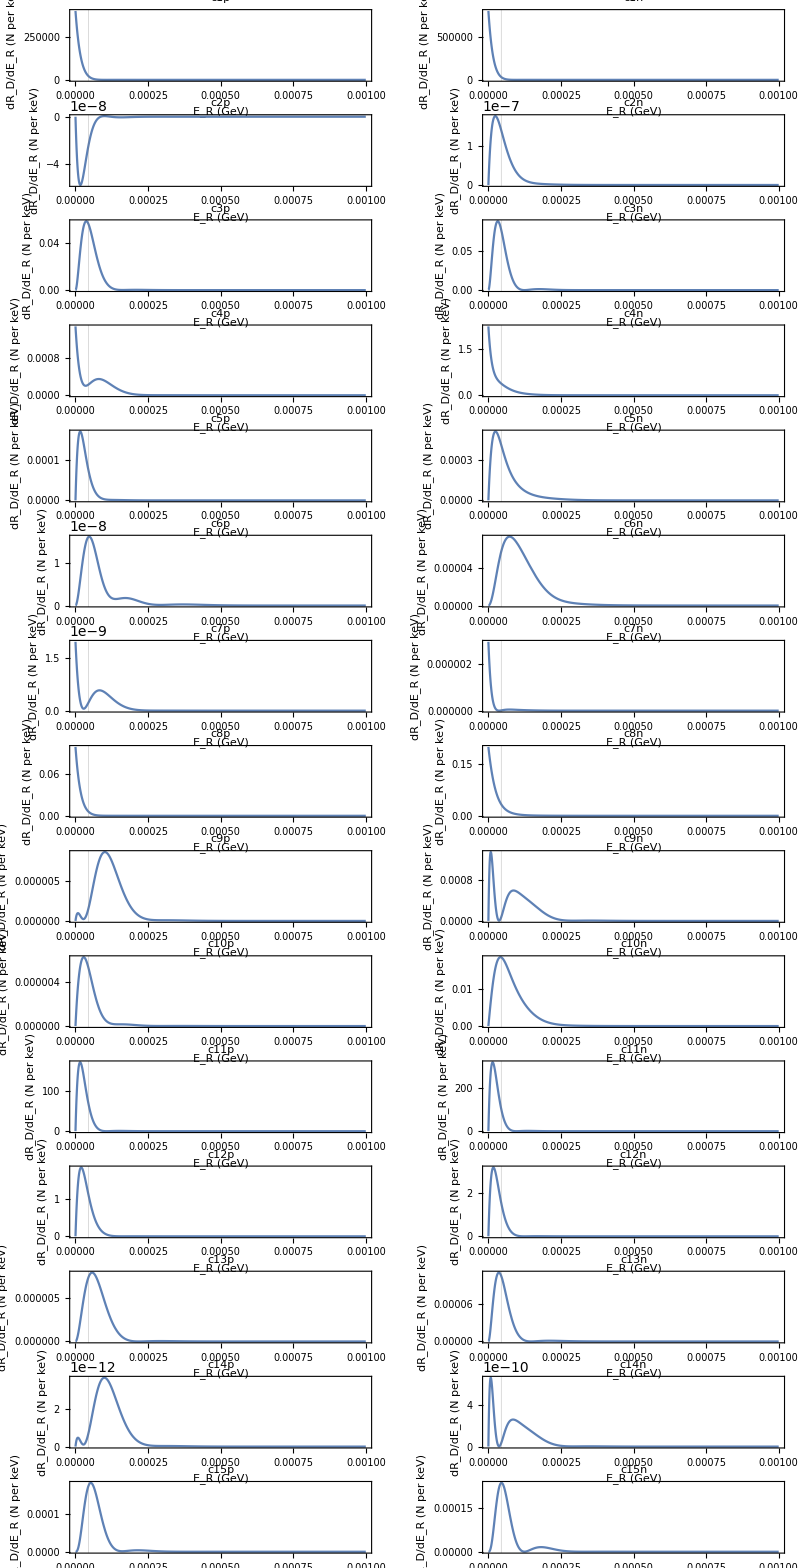

```mathematica
GraphicsGrid[ArrayReshape[plots,{15,2}],ImageSize->Full]
```